```mathematica
(* V -> top left right bottom *)
(* H -> left top bottom right *)
```

```mathematica
ClearAll;
```

```mathematica
mpsToMpdoH[tensor_] :=Flatten[SparseArray[{l2_,b_,r2_,l1_,t_,r1_}->Indexed[Normal[tensor],{l2,b,r2}]*Indexed[Normal[tensor],{l1,t,r1}]*,
Join[Dimensions[tensor],Dimensions[tensor]]],
{{4,1},{5},{2},{6,3}}];
```

```mathematica
spinWave[tensor_,perturbation_,p_]:=(1-p)*tensor + p*perturbation.tensor;
```

```mathematica
tensorGHZH=SparseArray[{l_,b_,r_}/;l==b==r->1,{2,2,2},0];
```

```mathematica
spec = {E^(-2 b),E^(2 b),E^(2 b),E^(-2 b)};
(* sigmaX = {{0, 1},{1, 0}}; *)
sigmaX = SparseArray[{{1,2} -> 1, {2,1} -> 1},{2,2},0];
```

```mathematica
sigmaZ = SparseArray[{{1,1} -> 1, {2,2} -> -1},{2,2},0];
```

```mathematica
toRightV = SparseArray[{i_,mu_, k_} /;i== k && mu==k->  1,{2,2,2},0];
```

```mathematica
toLeftV= SparseArray[{j_, mu_,l_} /;j==l -> Indexed[spec,mu*l],{2,2,2},0];
```

```mathematica
idH[dim_]:=SparseArray[{mu_,i_, k_,nu_} /;i== k && mu==nu->  1,{dim,2,2,dim},0];
```

```mathematica
tensorIsingV = toLeftV.toRightV;
```

```mathematica
(*tensorIsingV= SparseArray[{i_,mu_,nu_,k_} /;2(k-1)+(nu-1) == 2(mu-1) + (i-1) ->  Indexed[spec,2(k-1)+nu],{2,2,2,2},0];*)
```

```mathematica
Transpose[toRightV,{1,3,2}].Transpose[toLeftV,{2,1,3}]//MatrixForm
```

((ⅇ^(-2 b) | 0
0 | ⅇ^(2 b)) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (ⅇ^(2 b) | 0
0 | ⅇ^(-2 b)))

```mathematica
tensorTrotterIsingV =MatrixExp[h sigmaX /2].tensorIsingV.MatrixExp[h sigmaX /2];
```

```mathematica
KroneckerProduct[MatrixExp[h sigmaX /2],MatrixExp[h sigmaX/2 ]].DiagonalMatrix[spec].KroneckerProduct[MatrixExp[h sigmaX /2],MatrixExp[h sigmaX/2 ]]//Simplify//MatrixForm
```

(1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)+6 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))-2 ⅇ^(4 b+2 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)-2 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))+6 ⅇ^(4 b+2 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)-2 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))+6 ⅇ^(4 b+2 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)+6 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))-2 ⅇ^(4 b+2 h)))

```mathematica
Transpose[MatrixExp[h sigmaX /2].toRightV.MatrixExp[h sigmaX /2],{1,3,2}].Transpose[MatrixExp[h sigmaX /2].toLeftV.MatrixExp[h sigmaX /2],{2,1,3}]//Simplify//MatrixForm
```

((1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)+6 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))-2 ⅇ^(4 b+2 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)-2 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))+6 ⅇ^(4 b+2 h))) | (1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)))
(1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h))) | (1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)-2 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))+6 ⅇ^(4 b+2 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 (b+h)) (1+ⅇ^(4 b)+6 ⅇ^(2 h)+ⅇ^(4 h)+ⅇ^(4 (b+h))-2 ⅇ^(4 b+2 h))))

```mathematica
tensorTrotterIsing2V =Flatten[tensorIsingV.MatrixExp[h sigmaX ].tensorIsingV,{{1},{2,4},{3,5},{6}}]/.b->b/2;
```

```mathematica
(* tensorTrotterIsingV  - Normal[SparseArray[{i_,mu_,nu_,k_} ->Sum[Indexed[Indexed[E^(h sigmaX),{i,p}]*toLeft,{p,mu,l}]*Indexed[toRight,{l,nu,k}],{l,1,2},{p,1,2}],{2,4,4,2}] ] *)
```

```mathematica
tensorIsingH = Transpose[tensorIsingV,{2,1,4,3}];
```

```mathematica
tensorTrotterIsingH = Transpose[tensorTrotterIsingV,{2,1,4,3}];
```

```mathematica
tensorTrotterIsing2H = Transpose[tensorTrotterIsing2V,{2,1,4,3}];
```

```mathematica
tensorIsingChainH[l_] := If[l>1, tensorIsingChainH[l-1].tensorIsingH,tensorIsingH];
```

```mathematica
tensorTrotterIsingChainH[l_] := If[l>1, tensorTrotterIsingChainH[l-1].tensorTrotterIsingH,tensorTrotterIsingH];
```

```mathematica
tensorChainH[tensor_,l_]:=If[l>1, tensorChainH[tensor,l-1].tensor,tensor];
```

```mathematica
idMPOH[l_,dim_]:=If[l>1, idMPOH[l-1,dim].idH[dim],idH[dim]];
```

```mathematica
(* generatorsIsing[l_] :=Transpose[Flatten[tensorIsingChainH[l],  {{1},Table[2j,{j,1,l}],Table[2k+1,{k,1,l}],{2l+2}} ], RotateLeft[Table[i,{i,4}]]]; *)
```

```mathematica
(* generatorsTrotterIsing[l_] := Transpose[Flatten[tensorTrotterIsingChainH[l],  {{1},Table[2j,{j,1,l}],Table[2k+1,{k,1,l}],{2l+2}} ], RotateLeft[Table[i,{i,4}]]]; *)
```

```mathematica
generators[tensor_,l_]:=Flatten[tensorChainH[tensor,l],  {{2l+2},{1},Table[2j,{j,1,l}],Table[2k+1,{k,1,l}]} ];
```

```mathematica
generatorsIsing[l_] :=Flatten[tensorIsingChainH[l],  {{2l+2},{1},Table[2j,{j,1,l}],Table[2k+1,{k,1,l}]} ];
```

```mathematica
generatorsTrotterIsing[l_] :=Flatten[tensorTrotterIsingChainH[l],  {{2l+2},{1},Table[2j,{j,1,l}],Table[2k+1,{k,1,l}]} ];
```

```mathematica
generatorsIsing[2]//MatrixForm
```

((ⅇ^(-4 b) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ⅇ^(4 b) | 0
0 | 0 | 0 | 0) | (1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1) | (0 | 0 | 0 | 0
0 | ⅇ^(4 b) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-4 b)))

```mathematica
generatorsTrotterIsing[2]//MatrixForm
```

((ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(-4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2) | ((-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+(ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)
2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+(ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2)
((-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+(ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | 2 (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+(-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+(ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4) | (ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(-4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4))

```mathematica
gti2= generatorsTrotterIsing[2];
```

```mathematica
gti2[[1,1]]//MatrixForm
```

(ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(-4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2)

```mathematica
gti2[[2,2]]//MatrixForm
```

(ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2) | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^4+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3
ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2 | ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3+ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^3 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)+ⅇ^(-4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^3 | ⅇ^(4 b) (-1/2 ⅇ^(-h/2)+ⅇ^(h/2)/2)^2 (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^2+ⅇ^(-4 b) (ⅇ^(-h/2)/2+ⅇ^(h/2)/2)^4)

```mathematica
gti2[[2,1]]//MatrixForm//Simplify
```

(1/8 ⅇ^(-2 h) (-1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^3 (1+ⅇ^h) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2
1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (-1+ⅇ^h) (1+ⅇ^h)^3
1/8 ⅇ^(-2 h) (-1+ⅇ^h)^3 (1+ⅇ^h) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (-1+ⅇ^h) (1+ⅇ^h)^3 | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (1+ⅇ^h)^2 (1+ⅇ^(2 h)))

```mathematica
gti2[[1,2]]//MatrixForm//Simplify
```

(1/8 ⅇ^(-2 h) (1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^h) (1+ⅇ^h)^3 | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2
1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^3 (1+ⅇ^h)
1/8 ⅇ^(-2 h) (-1+ⅇ^h) (1+ⅇ^h)^3 | 1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (1+ⅇ^h)^2 (1+ⅇ^(2 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h))
1/8 ⅇ^(-2 h) (-1+ⅇ^(2 h))^2 | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^3 (1+ⅇ^h) | 1/8 ⅇ^(-2 h) (-1+ⅇ^(4 h)) | 1/8 ⅇ^(-2 h) (-1+ⅇ^h)^2 (1+ⅇ^(2 h)))

```mathematica
gti2[[1,2]]-gti2[[2,1]]//MatrixForm//Simplify
```

(1/2 ⅇ^-h (1+ⅇ^(2 h)) | 0 | 1/2 ⅇ^-h (-1+ⅇ^(2 h)) | 0
0 | -1/2 ⅇ^-h (1+ⅇ^(2 h)) | 0 | -1/2 ⅇ^-h (-1+ⅇ^(2 h))
1/2 ⅇ^-h (-1+ⅇ^(2 h)) | 0 | 1/2 ⅇ^-h (1+ⅇ^(2 h)) | 0
0 | -1/2 ⅇ^-h (-1+ⅇ^(2 h)) | 0 | -1/2 ⅇ^-h (1+ⅇ^(2 h)))

```mathematica
gti2[[1,2]].gti2[[2,1]]-gti2[[2,1]].gti2[[1,2]]//MatrixForm//Simplify
```

(0 | 1/4 ⅇ^(-3 h) (-1+ⅇ^h) (1+ⅇ^h) (1+ⅇ^(4 h)) | 0 | 1/4 ⅇ^(-3 h) (-1+ⅇ^(2 h))^2 (1+ⅇ^(2 h))
-1/4 ⅇ^(-3 h) (-1+ⅇ^h) (1+ⅇ^h) (1+ⅇ^(4 h)) | 0 | -1/4 ⅇ^(-3 h) (-1+ⅇ^(2 h))^2 (1+ⅇ^(2 h)) | 0
0 | 1/4 ⅇ^(-3 h) (-1+ⅇ^(2 h))^2 (1+ⅇ^(2 h)) | 0 | 1/4 ⅇ^(-3 h) (-1+ⅇ^h) (1+ⅇ^h) (1+ⅇ^(4 h))
-1/4 ⅇ^(-3 h) (-1+ⅇ^(2 h))^2 (1+ⅇ^(2 h)) | 0 | -1/4 ⅇ^(-3 h) (-1+ⅇ^h) (1+ⅇ^h) (1+ⅇ^(4 h)) | 0)

```mathematica
Dimensions[tensorChainH[tensorTrotterIsing2V,2]]
```

{2,4,4,4,4,2}

```mathematica
gtit2=generators[tensorTrotterIsing2H,2];
```

```mathematica
gtit2//MatrixForm
```

((ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0) | (ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0) | (ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0) | ((ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0)
(0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0) | (0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-4 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0) | (0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0) | (0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0) | (0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0) | (0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0) | (0 | 0 | 0 | 0
ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0)
(0 | 0 | 0 | 0
0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2) | (0 | 0 | 0 | 0
0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2) | (0 | 0 | 0 | 0
0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2) | (0 | 0 | 0 | 0
0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2))

```mathematica
gi4=generatorsIsing[4];
```

```mathematica
uI4 = SparseArray[{i_,j_}/;j==2i-1||i==8+j/2->1,{16,16}];
```

```mathematica
gi4t=Table[(uI4.(gi4[[i,j]]).uI4†),{i,2},{j,2}]//MatrixForm
```

((ⅇ^(-8 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(8 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | (ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(4 b) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(4 b) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(4 b) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(4 b) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-4 b)) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(8 b) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-8 b)))

```mathematica
krausProj[dim_, dmat_]:= Module[{k=1,dimBlock=0,ans={},c,c1,tr,dimSum=Sum[Indexed[dim,j]*Length[Indexed[dmat,j]],{j,1,Length[dim]}],kthNorm},
While[k≤ Length[dim],
kthNorm = Sqrt[Length[Indexed[dmat,k]]];
For[j=1,j<Length[Indexed[dmat,k]],++j,
c1=SparseArray[{l_,l_}/;dimBlock+(j-1)*Indexed[dim,k]<l≤dimBlock+j*Indexed[dim,k]->1,{dimSum,dimSum},0];
ans=Append[ans,c1/kthNorm];
For[i=j+1,i≤ Length[Indexed[dmat,k]],++i,
c=SparseArray[{l_,m_}/;dimBlock+(i-1)*Indexed[dim,k]<l≤dimBlock+i*Indexed[dim,k]&&
dimBlock+(j-1)*Indexed[dim,k]<m≤dimBlock+j*Indexed[dim,k]&&
Mod[l-m,Indexed[dim,k]]==0->
Sqrt[Indexed[dmat,{k,i}]/Indexed[dmat,{k,j}]],{dimSum,dimSum},0];
ans=Append[ans,c/kthNorm];
c=SparseArray[{l_,m_}/;dimBlock+(j-1)*Indexed[dim,k]<l≤dimBlock+j*Indexed[dim,k]&&
dimBlock+(i-1)*Indexed[dim,k]<m≤dimBlock+i*Indexed[dim,k]&&
Mod[l-m,Indexed[dim,k]]==0->
Sqrt[Indexed[dmat,{k,j}]/Indexed[dmat,{k,i}]],{dimSum,dimSum},0];
ans=Append[ans,c/kthNorm];
]
];
c1=SparseArray[{l_,l_}/;dimBlock+(Length[Indexed[dmat,k]]-1)*Indexed[dim,k]<l≤dimBlock+Length[Indexed[dmat,k]]*Indexed[dim,k]->1,{dimSum,dimSum},0];
ans=Append[ans,c1/kthNorm];
dimBlock+=Length[Indexed[dmat,k]]*Indexed[dim,k];
++k;
];
ans
] ;
```

```mathematica
psps= krausProj[{2,1,1},{{1,2,3},{1},{1,2}}]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
Sum[psps[[i]].Array[Subscript[a, ##]&,{9,9}].psps[[i]]†,{i,Length[psps]}]//MatrixForm
```

((a_(1,1))/3+(a_(3,3))/6+(a_(5,5))/9 | (a_(1,2))/3+(a_(3,4))/6+(a_(5,6))/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(a_(2,1))/3+(a_(4,3))/6+(a_(6,5))/9 | (a_(2,2))/3+(a_(4,4))/6+(a_(6,6))/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 a_(1,1))/3+(a_(3,3))/3+(2 a_(5,5))/9 | (2 a_(1,2))/3+(a_(3,4))/3+(2 a_(5,6))/9 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 a_(2,1))/3+(a_(4,3))/3+(2 a_(6,5))/9 | (2 a_(2,2))/3+(a_(4,4))/3+(2 a_(6,6))/9 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a_(1,1)+(a_(3,3))/2+(a_(5,5))/3 | a_(1,2)+(a_(3,4))/2+(a_(5,6))/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | a_(2,1)+(a_(4,3))/2+(a_(6,5))/3 | a_(2,2)+(a_(4,4))/2+(a_(6,6))/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a_(7,7) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (a_(8,8))/2+(a_(9,9))/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a_(8,8)+(a_(9,9))/2)

```mathematica
xMPOId[x_,l_] := Module[{chain = x[l-1]},Flatten[x[l-1].idMPOH[2,Length[chain]],
{Join[Table[2j,{j,1,l-1}],{2l}],
{1},{2l+1},{2(l+1)},{2l+4},
Join[Table[2k+1,{k,1,l-1}],{2(l+1)+1}]}]];
```

```mathematica
reshapeMPDOforKraus[mpoH_,l_]:=Flatten[mpoH[l],
{Table[2j,{j,1,l}],
{1},{2l+2},
Table[2k+1,{k,1,l}] }];
```

```mathematica
cX[dim_,dmat_,u_,x_,l_]:= Module[{kP=krausProj[dim,dmat],one,p},
(one.xMPOId[x,l].one/.one->IdentityMatrix[Length[u]])-
(Sum[p.xMPOId[x,l].p†/.p->u.Indexed[kP,i].u†,{i,Length[kP]}])
];
```

```mathematica
cXtest[dim_,dmat_,u_,x_,l_]:= Module[{kP=krausProj[dim,dmat],one,p},
(one.reshapeMPDOforKraus[x,l].one/.one->IdentityMatrix[Length[u]])-
(Sum[p.reshapeMPDOforKraus[x,l].p†/.p->u.Indexed[kP,i].u,{i,Length[kP]}])
];
```

```mathematica
cXtest[{1,1,1,1},{{1},{1},{1},{1}},IdentityMatrix[4],tensorIsingChainH,2]
```

{{{{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0}}}}

```mathematica
(* Refine[cXtest[{1,1,1,1},{{ⅇ^(-8 b),1,1,1},{1,1,ⅇ^(8 b),1},{1,ⅇ^(8 b),1,1},{1,1,1,ⅇ^(-8 b)}},uI4,tensorIsingChainH,4],b>0] *)
```

```mathematica
MatrixRank[Refine[Flatten[cX[{1,1,1,1},{{1},{1},{1},{1}},IdentityMatrix[4],tensorIsingChainH,2],{{1,6,2},{3,4,5}}],b>0]]
```

4

```mathematica
MatrixRank[Refine[Flatten[cX[{1,1,1,1},{{ⅇ^(-8 b),1,1,1},{1,ⅇ^(8 b),1,1},{1,1,ⅇ^(8 b),1},{1,1,1,ⅇ^(-8 b)}},uI4†,tensorIsingChainH,4],{{1,6,2},{3,4,5}}],b>0]]
```

6

```mathematica
2(2^2-1)
```

6

```mathematica
(* Joint block diagonlization *)
appendMatrixEven[a_]:=If[Mod[Length[a],2]==0,a,SparseArray[{i_,j_}/;i≤ Length[a]&&j≤ Length[a]->Indexed[a,{i,j}],{Length[a]+1,Length[a]+1},0]];
rotationToDiag[a_,i_,j_]:=Module[{u,submatrix ={{Indexed[a,{i,i}],Indexed[a,{i,j}]},{Indexed[a,{j,i}],Indexed[a,{j,j}]}}},

u=Normalize /@ Eigenvectors[submatrix];
SparseArray[{(*{k_,l_}/;k≠ i&&l≠ j&&k==l->1,*)
{i,i}->Indexed[u,{1,1}], 
{i,j}->Indexed[u,{1,2}],
{j,i}->Indexed[u,{2,1}],
{j,j}->Indexed[u,{2,2}]},
{Length[a],Length[a]},0]
]
```

```mathematica
appendMatrixEven[{{1}}]//MatrixForm
```

(1 | 0
0 | 0)

```mathematica
Normalize /@ Eigenvectors[{{1,2},{2,4}}]//MatrixForm
```

(1/(√5) | 2/(√5)
-2/(√5) | 1/(√5))

```mathematica
rotationToDiag[{{1,2},{2,4}},1,2]//MatrixForm
```

(1/(√5) | 2/(√5)
-2/(√5) | 1/(√5))

```mathematica
{{1,2,0},{2,4,5},{0,5,6}}//MatrixForm
```

(1 | 2 | 0
2 | 4 | 5
0 | 5 | 6)

```mathematica
rotationToDiag[{{1,2,3},{2,4,5},{3,5,6}},2,3].{{1,2,3},{2,4,5},{3,5,6}}.(rotationToDiag[{{1,2,3},{2,4,5},{3,5,6}},2,3]†)//Simplify//MatrixForm
```

(0 | 0 | 0
0 | 5+√26 | 0
0 | 0 | 5-√26)

```mathematica
findEquivalentBD[a_,q_,error_]:=Module[{i,j,k,unchecked= Table[m,{m,Length[q]}],bigQ={},dims={},p,currentClass,bigP={},tryForZero},
While[unchecked≠ {},
currentClass =Graph[{Indexed[unchecked,1]},{}];
p={IdentityMatrix[Length[Indexed[q,Indexed[unchecked,1]]]]};
unchecked=Delete[unchecked,1];
For[i=1, i≤ VertexCount[currentClass],++i,
For[j=1,j≤ Length[unchecked],++j,
For[k=1,k≤ Length[a],++k,
tryForZero=Indexed[q,Indexed[VertexList[currentClass],i]].Indexed[a,k].Indexed[q,Indexed[unchecked,j]]†;
If[Norm[tryForZero,"Frobenius"]>error,
currentClass=GraphUnion[currentClass,Graph[{Indexed[VertexList[currentClass],i]<->Indexed[unchecked,j]}]];
AppendTo[p,tryForZero.Indexed[p,i]/Sqrt[Indexed[tryForZero†.tryForZero,{1,1}]]];
unchecked=Delete[unchecked,j];
Break[];
];
];
];
];
For[j=1,j≤ VertexCount[currentClass],++j,
bigQ=Join[bigQ,Indexed[q,Indexed[VertexList[currentClass],j]]]
];
p=SparseArray[Band[{1,1}]->p];
AppendTo[dims,currentClass];
AppendTo[bigP,p];
];
bigP=SparseArray[Band[{1,1}]->Normal[bigP]];
{bigQ,dims,bigP}
];
```

```mathematica
blockDiagonalizeMurota[a_,rand_,error_]:=Module[{i,j,(*rand,*) dim=Length[Indexed[a,1]],q={},u,(* u1 *),evectors,evalues,evaluesDistinct,bigP,dims,dim1=1(*,ans={},currentDim=0*)},
(*For[i=0,i<iter,++i,*)
(*rand = Table[RandomReal[],Length[a]];*)
{evalues,evectors}=Eigensystem[Sum[Indexed[rand,j]*Indexed[a,j],{j,Length[a]}]];
{evalues,evectors}=SortBy[{evalues,evectors},First];
evaluesDistinct=Gather[Rationalize[evalues,error]];
For[j=1, j≤ Length[evaluesDistinct],++j,
AppendTo[q,Orthogonalize[Table[Indexed[evectors,k],{k,dim1,dim1+Length[Indexed[evaluesDistinct,j]]-1}]]];
dim1+=Length[Indexed[evaluesDistinct,j]];
];
(*Print[evectors.Sum[Indexed[rand,j]*Indexed[a,j],{j,Length[a]}].evectors†//MatrixForm];*)
{u,dims,bigP}=findEquivalentBD[a,q,error];
{bigP.u,dims,bigP}
(*];
If[i==iter,ans={Identity[dim],dim},
ans= {Identity[dim],{}};
For[j=1,j≤ Length[dims],j++,
{u1,dim1}=blockDiagonalizeMurota[block(a),iter];
Indexed[ans,1]= Indexed[ans,1].(IdentityMatrix[dim]+
SparseArray[{i_,j_}/; currentDim<i<currentDim+Indexed[dims,j],currentDim<j<currentDim+Indexed[dims,j]->
Indexed[u1,{i-currentDim,j-currentDim}]-If[i==j,1,0]]);
currentDim+=Indexed[dims,j];
]
];
ans *)
]
```

```mathematica
blockDiagonalizeMurota[a_]:=blockDiagonalizeMurota[a,Table[RandomReal[],Length[a]],10^(-6)];
```

```mathematica
ququq={IdentityMatrix[5],{{0,1,0,0,0},{1,0,0,0,0},{0,0,-1,0,0},{0,0,0,1,0},{0,0,0,0,2}},{{1,0,0,0,0},{0,-1,0,0,0},{0,0,0,1,0},{0,0,1,0,0},{0,0,0,0,0}}};
Table[ququq[[i]]//MatrixForm,{i,Length[ququq]}]
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 2),(1 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)}



{{{0.,0.,0.,0.,1.},{0.93787,0.346987,0.,0.,0.},{0.,0.,0.417818,0.908531,0.},{-0.346987,0.93787,0.,0.,0.},{0.,0.,-0.908531,0.417818,0.}},{-Graphics-,-Graphics-},SparseArray[…]}

```mathematica
{uququq,dimququq,zququq}=blockDiagonalizeMurota[ququq]
```

```mathematica
Chop[Table[uququq.ququq[[i]].uququq†//MatrixForm,{i,Length[ququq]}]]
```

{(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.),(2. | 0 | 0 | 0 | 0
0 | 0.650857 | 0 | 0.759201 | 0
0 | 0 | 0.650857 | 0 | 0.759201
0 | 0.759201 | 0 | -0.650857 | 0
0 | 0 | 0.759201 | 0 | -0.650857),(0 | 0 | 0 | 0 | 0
0 | 0.759201 | 0 | -0.650857 | 0
0 | 0 | 0.759201 | 0 | -0.650857
0 | -0.650857 | 0 | -0.759201 | 0
0 | 0 | -0.650857 | 0 | -0.759201)}

```mathematica
blblb={IdentityMatrix[3],{{0,1,0},{1,0,0},{0,0,1}},{{-1,0,0},{0,0,1},{0,1,0}},{{1,0,0},{0,0,0},{0,0,-1}}};
Table[blblb[[i]]//MatrixForm,{i,Length[blblb]}]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1),(-1 | 0 | 0
0 | 0 | 1
0 | 1 | 0),(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1)}


{{{0.0134931,0.730638,0.682632},{0.0924925,-0.680679,0.726719},{-0.995622,-0.0533327,0.076763}},{-Graphics-},SparseArray[…]}

```mathematica
{ublbl,dimblbl,zblbl}=blockDiagonalizeMurota[blblb]
```

```mathematica
ublbl.ublbl†//MatrixForm
```

(1. | 0. | 0.
0. | 1. | -2.77556×10^-17
0. | -2.77556×10^-17 | 1.)

```mathematica
Chop[Table[ublbl.blblb[[i]].ublbl†//MatrixForm,{i,Length[blblb]}]]
```

{(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.),(0.485703 | 0.554476 | -0.675758
0.554476 | 0.402206 | 0.728551
-0.675758 | 0.728551 | 0.112091),(0.997331 | 0.0650675 | 0.0331134
0.0650675 | -0.99788 | 0.00107874
0.0331134 | 0.00107874 | -0.999451),(-0.465804 | -0.494834 | -0.0658349
-0.494834 | -0.519566 | -0.147873
-0.0658349 | -0.147873 | 0.985371)}

```mathematica
ghohoho = {gti2[[1,1]],gti2[[1,2]],gti2[[2,1]],gti2[[2,2]]}/.h->1/.b->1;
```

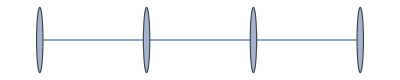
{{{-0.428161,-0.530682,-0.585652,-0.438254},{0.0166398,0.727825,-0.685318,0.0182309},{0.551513,0.110983,0.109458,-0.819472},{-0.715706,0.419917,0.418771,-0.368871}},{-Graphics-},SparseArray[…]}

```mathematica
{uhoho,dimhoh,zhoho}=blockDiagonalizeMurota[ghohoho]
```

```mathematica
Chop[Table[uhoho.ghohoho[[i]].uhoho†//MatrixForm,{i,4}]]
```

{(106.722 | 49.8589 | -0.920119 | -0.690507
49.8589 | 23.3016 | -0.422568 | -0.329028
-0.920119 | -0.422568 | 0.0144607 | 0.000201707
-0.690507 | -0.329028 | 0.000201707 | 0.00953546),(3.69487 | 0.845819 | -0.819143 | 0.669772
0.845819 | 0.429392 | 0.0233244 | -0.0324491
-0.819143 | 0.0233244 | 0.370148 | -0.314615
0.669772 | -0.0324491 | -0.314615 | 0.267786),(3.57094 | -1.09046 | 0.996019 | 0.212854
-1.09046 | 0.580158 | -0.0300035 | -0.00111554
0.996019 | -0.0300035 | 0.581895 | 0.130228
0.212854 | -0.00111554 | 0.130228 | 0.0291993),(98.4962 | -55.7147 | -0.963061 | -0.755169
-55.7147 | 31.5241 | 0.554697 | 0.429479
-0.963061 | 0.554697 | 0.0204409 | 0.00995272
-0.755169 | 0.429479 | 0.00995272 | 0.00638849)}

```mathematica
SparseArray[Band[{1,1}]->{{{1,2},{2,1}},{{3}}}]//MatrixForm
```

(1 | 2 | 0
2 | 1 | 0
0 | 0 | 3)

```mathematica
SparseArray[Band[{1,1}]->Normal[{SparseArray[{1,1}->3],{{1,2},{2,1}}}]]//MatrixForm
```

(3 | 0 | 0
0 | 1 | 2
0 | 2 | 1)

```mathematica
Table[Refine[generatorsTrotterIsing[4][[Quotient[i+1,2],Mod[i,2]+1]]-generatorsTrotterIsing[4][[Quotient[i+1,2],Mod[i,2]+1]]†,{Element[h,Reals],Element[b,Reals]}]//MatrixForm,{i,4}]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
gti4=Table[generatorsTrotterIsing[4][[Quotient[i+1,2],Mod[i,2]+1]],{i,4}]/.h->10/.b->1;
```

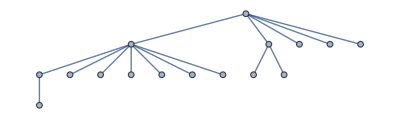
{{{-0.25,-0.250002,-0.249998,-0.25,-0.250001,-0.250004,-0.249999,-0.250002,-0.249998,-0.250001,-0.249996,-0.249999,-0.25,-0.250002,-0.249998,-0.25},{0.000262349,0.247939,-0.251515,-0.00383885,0.252306,0.499983,0.000528555,0.248205,-0.248209,-0.00053244,-0.499987,-0.25231,0.00383508,0.251512,-0.247943,-0.000266121},{0.188545,-0.137426,0.326243,0.000265922,0.325385,-0.000568913,0.463074,0.137113,-0.137106,-0.463099,0.000609013,-0.325391,-0.000271971,-0.326249,0.137433,-0.188551},{-1.81113×10^-6,0.252053,0.247913,0.499985,-0.2482,0.0038372,-0.000284834,0.25177,-0.25177,0.000284995,-0.00383735,0.248235,-0.499985,-0.247948,-0.252053,0.},{-0.463078,-0.325749,-0.137232,0.000113578,-0.137292,0.0000434907,0.188533,0.325886,-0.325901,-0.188563,-0.0000474593,0.137307,-0.0000976555,0.137247,0.325735,0.463095},{-0.349153,0.328436,-0.0520711,-0.119781,0.203504,-0.483168,0.324929,0.147313,-0.0424808,0.032407,0.190281,0.0123467,0.228014,0.0824323,-0.503009,0.},{0.226134,0.0753862,0.0753764,-0.0753826,0.0753756,-0.0753727,-0.0753726,-0.226132,0.0753857,-0.0753732,-0.0753727,-0.226142,-0.0753845,-0.226143,-0.226133,0.829151},{0.102553,-0.422326,0.223998,0.0111838,-0.431378,0.170339,0.143712,0.201936,0.0981717,0.135748,-0.177103,0.0277815,0.471546,-0.124664,-0.431499,0.},{-0.0189437,-0.220991,-0.315796,-0.13399,0.140614,0.0249654,0.164116,0.360005,0.243037,0.536674,0.122349,-0.21238,-0.351094,-0.354282,0.0157172,0.},{0.133784,-0.293008,-0.0551449,-0.249639,0.317123,0.173482,-0.232686,0.206066,0.153715,-0.378607,0.247074,0.441839,-0.206317,0.0998648,-0.357547,0.},{0.0342888,0.142758,0.0249878,-0.246706,-0.10843,-0.205994,0.307089,0.0520194,0.432561,-0.116006,-0.619202,0.347297,-0.205807,0.0266129,0.134532,0.},{0.368027,0.276637,-0.225214,-0.14323,-0.209622,-0.269093,-0.346962,0.549446,-0.0704822,-0.183038,0.0325353,-0.0552337,0.263064,-0.175485,0.188649,0.},{0.26334,0.149395,-0.0537032,-0.358537,-0.489235,0.16607,0.367788,-0.0451177,-0.0826257,-0.076843,0.344635,-0.185653,-0.280848,0.35072,-0.0693852,0.},{-0.0470324,-0.155443,-0.117867,0.500282,-0.0851218,-0.186067,-0.0641681,0.155429,0.489635,-0.276075,0.0152762,-0.408759,-0.110552,0.370648,-0.0801845,0.},{-0.515034,0.276705,0.413512,-0.282611,-0.120792,0.318451,-0.254222,0.163972,0.322302,-0.113221,0.10785,-0.209494,-0.014659,-0.153763,0.061005,0.},{0.110685,-0.202333,0.535782,-0.216781,0.130788,-0.331928,-0.23628,0.210104,-0.212485,0.298429,-0.152063,-0.161216,-0.196893,0.403722,0.0204695,0.}},{-Graphics-},SparseArray[…]}

```mathematica
{ut4,dt4,zt4}=blockDiagonalizeMurota[gti4]
```

```mathematica
Chop[Table[ut4.gti4[[i]].ut4†//MatrixForm,{i,4}],10^(-7)]
```

{(3.21398×10^18 | 9.66268×10^13 | -1.66645×10^14 | 8.93398×10^11 | 1.28777×10^13 | -5.76949×10^9 | -2.66013×10^9 | -3.76948×10^9 | 6.16482×10^8 | 7.0167×10^9 | -8.44772×10^9 | 3.38966×10^9 | 5.28728×10^9 | 1.06526×10^9 | 1.09492×10^10 | -7.53541×10^9
9.66268×10^13 | 1.12427×10^10 | -1.32703×10^9 | -3.24765×10^9 | 1.02496×10^8 | 2409.74 | -22527.4 | -128906. | 128955. | 193492. | -14002.9 | 51212.7 | -170285. | -149139. | -53692.4 | -251414.
-1.66645×10^14 | -1.32703×10^9 | 1.17101×10^10 | -1.16732×10^7 | -8.78334×10^7 | 425624. | 161878. | 262187. | 25132.4 | -544492. | 629419. | -241502. | -346205. | -83974.7 | -756295. | 520924.
8.93398×10^11 | -3.24765×10^9 | -1.16732×10^7 | 3.26416×10^9 | 890882. | -39355.7 | 5275.39 | 102701. | -123012. | -145609. | -40443.6 | -28648.4 | 201566. | 153758. | 123033. | 199320.
1.28777×10^13 | 1.02496×10^8 | -8.78334×10^7 | 890911. | 1.94617×10^9 | 29116.7 | -68451.8 | -19044.3 | 165041. | -98319. | 57449.5 | 3349.45 | 76655. | -18842.6 | 66564.4 | -45923.9
-5.76949×10^9 | 2393.52 | 425587. | -39386.6 | 29106. | -49.8805 | 20.3711 | -11.7576 | 16.5758 | -14.1099 | 29.3262 | -25.9558 | -39.0574 | -19.6041 | 22.2929 | 69.2928
-2.66013×10^9 | -22505.8 | 161903. | 5285.57 | -68384. | 24.2394 | -53.3817 | 8.01192 | 9.16096 | 0.726132 | -28.2672 | 19.4079 | 28.7076 | -0.992652 | -41.3746 | -31.5164
-3.76948×10^9 | -128887. | 262242. | 102770. | -19048.6 | -13.3009 | 15.59 | -5.53689 | 18.4599 | -22.4312 | -16.2744 | -37.3097 | -31.5158 | -12.8484 | -3.2975 | -28.2516
6.16482×10^8 | 129002. | 25137.7 | -123047. | 165027. | 16.9597 | -32.8992 | 67.5821 | 62.3314 | 58.4043 | 41.9653 | 22.1841 | 53.9473 | -9.09829 | 23.1741 | -17.867
7.01669×10^9 | 193536. | -544464. | -145588. | -98352.9 | -15.3521 | -15.9707 | -42.9048 | 27.4619 | 52.2839 | -24.9109 | -7.7845 | 22.0226 | -25.6799 | 52.8856 | -25.6767
-8.44772×10^9 | -13993.6 | 629407. | -40401.4 | 57446.4 | 32.6113 | -10.5315 | -20.5479 | 29.9621 | -21.6691 | 51.2401 | -0.31232 | -38.009 | 5.55827 | -54.6747 | 27.5199
3.38966×10^9 | 51170.4 | -241568. | -28640. | 3337.29 | -18.4311 | -0.90658 | -63.7028 | 46.7835 | -6.90607 | 37.1937 | -64.617 | -34.0819 | 6.7945 | 44.9348 | -15.0752
5.28728×10^9 | -170285. | -346182. | 201590. | 76699.6 | -72.0155 | 69.6472 | -22.8074 | 36.0913 | -4.99438 | -21.6936 | -45.2131 | -9.64906 | -7.42168 | 63.2738 | 3.70098
1.06526×10^9 | -149172. | -83984.7 | 153790. | -18808.2 | 5.70455 | 15.3987 | -11.1893 | -23.5378 | 2.43686 | 8.1975 | 24.9121 | 0.741019 | -10.3998 | 31.7999 | 2.34771
1.09492×10^10 | -53682.4 | -756255. | 123077. | 66603.6 | 54.6996 | -15.885 | -11.5091 | -6.20963 | 43.1469 | -50.1104 | 51.7307 | 70.6853 | 47.9699 | 32.3961 | -39.604
-7.53541×10^9 | -251410. | 520935. | 199260. | -45943.2 | 53.605 | 13.4731 | 1.05111 | 2.43545 | -18.9843 | -7.85071 | 6.15607 | 6.36248 | 11.4667 | -22.0213 | 58.1401),(4.39429×10^19 | 4.30948×10^15 | -6.16846×10^13 | 3.59944×10^13 | 4.76735×10^12 | 3.10621×10^9 | 1.50168×10^9 | 2.02567×10^9 | -3.32028×10^8 | -3.78276×10^9 | 4.54716×10^9 | -1.82972×10^9 | -2.84942×10^9 | -5.63498×10^8 | -5.90792×10^9 | 4.06107×10^9
4.30948×10^15 | 4.23241×10^11 | -5.78004×10^9 | 3.29048×10^9 | 4.46715×10^8 | 318896. | 152773. | 204622. | -31845.5 | -387457. | 467279. | -179433. | -303247. | -57791. | -608608. | 404961.
-6.16846×10^13 | -5.78004×10^9 | 3.11094×10^8 | -4.79931×10^7 | 3.572×10^7 | 3757.98 | 737.461 | -681.459 | 949.584 | -7202.1 | 5340.21 | -1834.48 | -1989.82 | -1917.56 | -6252.4 | 4111.35
3.59944×10^13 | 3.29048×10^9 | -4.7993×10^7 | 2.68207×10^8 | 3.70785×10^6 | -1363.7 | 13.1367 | 2132.36 | -2517.15 | 1625.05 | -3405.03 | -7689.44 | 12856. | -255.889 | 5259.91 | 9602.33
4.76735×10^12 | 4.46715×10^8 | 3.57195×10^7 | 3.70811×10^6 | 1.39087×10^8 | 250.49 | -1205.46 | -4246.92 | 848.3 | -8438.96 | 1580.84 | -294.271 | 2761.07 | -4436.21 | 903.408 | -1983.73
3.10621×10^9 | 318971. | 3755.64 | -1827.01 | 714.495 | -748.788 | -601.932 | 503.22 | -158.569 | 318.155 | 351.017 | 209.353 | 333.399 | 133.706 | -31.3382 | 466.916
1.50168×10^9 | 152984. | 444.534 | -226.444 | -1469.71 | -608.792 | -368.431 | -272.09 | 43.6385 | 231.25 | 141.411 | -50.0479 | -428.34 | -460.221 | -94.67 | 27.3919
2.02567×10^9 | 205183. | 437.472 | 1777.29 | -3966.16 | 635.177 | -137.474 | 311.56 | -336.712 | -583.075 | -29.1835 | 543.456 | 554.828 | 31.595 | -780.727 | 79.7966
-3.3203×10^8 | -32002.8 | 1199.01 | -1694.38 | 2089.7 | -293.426 | 383.898 | -52.8092 | -1120.2 | -549.956 | 311.966 | 268.981 | -163.338 | 38.8272 | 98.1581 | -952.846
-3.78276×10^9 | -387681. | -7045.3 | 1875.72 | -8297.62 | 63.5592 | -101.536 | -320.246 | -9.1306 | 8.21462 | -0.333881 | 15.0852 | -80.1508 | 187.316 | -91.6051 | 304.847
4.54715×10^9 | 468072. | 5378.83 | -3028.9 | 2433.35 | 247.325 | 105.478 | -139.426 | -60.5444 | -55.7727 | -113.653 | 53.0749 | -80.183 | 287.797 | -207.091 | 604.805
-1.82972×10^9 | -179171. | -2542.32 | -7750.79 | -595.271 | 204.121 | 151.744 | 375.947 | 616.168 | 147.283 | -87.553 | -616.339 | -12.6855 | 343.382 | 496.917 | -456.909
-2.84942×10^9 | -303661. | -2100.89 | 12160.5 | 2616.04 | 145.821 | -399.399 | -146.965 | 177.139 | -309.559 | -42.4668 | 29.944 | 128.952 | 100.167 | 542.864 | 204.706
-5.63496×10^8 | -57901.1 | -2144.48 | -13.1744 | -3796.09 | 73.0927 | -206.737 | 524.116 | -89.2464 | 311.326 | 596.897 | 423.587 | 8.47055 | -356.032 | 140.5 | 7.19976
-5.90792×10^9 | -608603. | -6188.11 | 5463.63 | 170.269 | -404.263 | -197.939 | -418.955 | 38.622 | -122.416 | -199.326 | 66.588 | 542.902 | -118.354 | 128.047 | 174.248
4.06107×10^9 | 405459. | 3278.18 | 9608.43 | -1010.35 | 248.328 | 326.826 | -247.188 | -433.213 | 87.2284 | 142.333 | -213.695 | 184.803 | 250.424 | 346.14 | -881.799),(4.39429×10^19 | -3.65688×10^15 | -4.63474×10^13 | -3.04921×10^13 | 3.58106×10^12 | 2.69481×10^9 | 1.19002×10^9 | 1.76451×10^9 | -2.83447×10^8 | -3.22351×10^9 | 3.89659×10^9 | -1.57364×10^9 | -2.43886×10^9 | -4.89088×10^8 | -5.0528×10^9 | 3.47582×10^9
-3.65688×10^15 | 3.04932×10^11 | 4.12636×10^9 | 2.29803×10^9 | -3.18832×10^8 | -231105. | -103347. | -153999. | 27008.8 | 283734. | -336423. | 129217. | 213604. | 35719.2 | 434139. | -297184.
-4.63474×10^13 | 4.12637×10^9 | 2.73388×10^8 | 3.46951×10^7 | 3.86351×10^7 | -6133.91 | -3109.43 | -1869.04 | 2587.5 | 7957.38 | -8411.83 | 3412.54 | 5324.82 | 3451.09 | 11105.4 | -7474.6
-3.04921×10^13 | 2.29803×10^9 | 3.46955×10^7 | 2.59881×10^8 | -2.68165×10^6 | 350.049 | 962.221 | 3424.8 | -3277.46 | -7418.04 | 2424.41 | 5911.47 | -5029.21 | 6119.8 | -1520.98 | -531.102
3.58106×10^12 | -3.18833×10^8 | 3.86343×10^7 | -2.6807×10^6 | 1.38862×10^8 | 2032.85 | -320.024 | 5008.72 | 4253.26 | 2355.27 | 1154.99 | -1108.82 | -964.552 | 3256.89 | -618.691 | 563.53
2.69481×10^9 | -231777. | -5213.98 | 413.11 | 2240.41 | -738.076 | -61.1925 | 378.137 | -161.257 | -386.525 | 483.906 | 395.646 | 47.1326 | -110.649 | -252.363 | 410.961
1.19002×10^9 | -103116. | -2646.87 | 1584.16 | -225.632 | 272.438 | -78.6334 | 467.58 | 169.21 | 555.059 | 349.96 | 137.059 | -169.357 | -63.8431 | -252.662 | -273.491
1.76452×10^9 | -153521. | -2627.93 | 3375.2 | 4653.7 | 301.772 | 190.777 | -319.674 | -217.216 | 3.61219 | 213.405 | -235.604 | -413.295 | 813.232 | 82.8591 | 630.182
-2.83449×10^8 | 26715.2 | 1986.6 | -3350.56 | 4603.95 | -74.2261 | 67.8327 | 289.577 | -765.407 | -605.433 | 194.669 | -567.631 | -424.218 | 127.182 | 335.987 | -209.899
-3.22351×10^9 | 283786. | 8402.65 | -8019.6 | 2506.47 | -155.654 | 563.497 | -365.452 | -324.472 | -296.272 | 303.242 | 278.334 | 226.445 | -65.0288 | 164.91 | 88.8987
3.89659×10^9 | -336159. | -8623.81 | 3043.99 | 2332.28 | 314.105 | -125.373 | -41.2155 | 141.733 | 429.196 | -701.398 | 376.368 | -103.833 | -79.6993 | -577.394 | 391.402
-1.57364×10^9 | 129025. | 3435.24 | 6212.76 | -615.567 | -29.7935 | 397.51 | -76.7188 | -270.829 | 534.16 | 731.788 | -59.4458 | -43.745 | -70.6156 | 120.973 | -109.573
-2.43886×10^9 | 213209. | 5413.68 | -4962.87 | -904.083 | -261.645 | -93.5161 | -235.798 | -369.517 | -61.7501 | 30.6315 | 472.083 | -192.656 | -271.555 | 508.078 | 95.3515
-4.89089×10^8 | 35790.4 | 2563.68 | 5846.36 | 3029.47 | -15.2537 | -74.189 | 911.58 | 539.313 | -211.755 | -447.924 | -185.598 | -121.447 | -49.5114 | 54.4811 | 111.649
-5.0528×10^9 | 434168. | 11708.9 | -1715.79 | 153.255 | -355.029 | -529.33 | -191.067 | 170.265 | 57.3197 | -350.346 | -14.262 | 499.858 | 166.379 | 182.58 | -4.77904
3.47582×10^9 | -296756. | -7477.84 | -570.192 | 1063.14 | -81.3088 | -69.9695 | -28.8259 | -2.60149 | 17.2707 | 267.052 | -328.873 | 117.257 | 143.355 | -37.7292 | 75.1827),(3.21398×10^18 | -4.88958×10^13 | 1.58744×10^14 | -4.90959×10^11 | -1.22671×10^13 | -2.43655×10^9 | -1.12944×10^9 | -1.59252×10^9 | 2.56375×10^8 | 2.9184×10^9 | -3.52231×10^9 | 1.42648×10^9 | 2.20725×10^9 | 4.3448×10^8 | 4.57849×10^9 | -3.14581×10^9
-4.88958×10^13 | 9.08157×10^9 | 1.26804×10^9 | -3.26704×10^9 | -9.80418×10^7 | -39755.8 | -16042.4 | 32550.4 | -53766.4 | -40111.6 | -49765.9 | 1434.61 | 111182. | 74032.7 | 97893. | 61263.9
1.58744×10^14 | 1.26804×10^9 | 1.09101×10^10 | 1.04003×10^7 | -2.60153×10^7 | -174919. | -65820.9 | -107495. | -13363.6 | 223580. | -257852. | 96649.2 | 140063. | 33941. | 307966. | -211928.
-4.90959×10^11 | -3.26704×10^9 | 1.04003×10^7 | 3.26399×10^9 | -814857. | 16566.2 | 5437.03 | -46856.4 | 55411.2 | 66583. | 16271.1 | 11717.6 | -89042.1 | -68885.8 | -53989.3 | -89434.2
-1.22671×10^13 | -9.80418×10^7 | -2.60153×10^7 | -814916. | 1.9414×10^9 | -11455.6 | 30687.4 | 8959. | -74578.6 | 46688.4 | -28240.5 | -7069.11 | -33076.1 | 8740.45 | -27716.3 | 18836.4
-2.43655×10^9 | -39753.9 | -174953. | 16519.8 | -11476.7 | -27.0648 | 38.5542 | -4.77717 | 30.1936 | -43.9376 | -21.6568 | -34.9923 | -73.9691 | 4.98857 | -1.09378 | 13.6337
-1.12944×10^9 | -16031.2 | -65807.3 | 5436.42 | 30712.8 | 55.4833 | -42.6014 | 50.843 | 25.88 | 0.808696 | 6.46791 | 32.7599 | 23.1218 | -50.4515 | -69.5604 | -33.9443
-1.59252×10^9 | 32545. | -107509. | -46843.6 | 8957.57 | 3.92477 | 14.593 | -47.3748 | 7.54577 | -9.29333 | 5.88575 | 0.88204 | 36.1128 | 61.438 | -42.1894 | -3.80719
2.56375×10^8 | -53789.1 | -13397.4 | 55467.1 | -74595.6 | 37.5567 | 4.92148 | -19.0365 | 2.15654 | 50.2115 | 25.7741 | 7.16543 | 25.6823 | -14.0348 | -4.81761 | -11.6413
2.9184×10^9 | -40111.4 | 223563. | 66580.6 | 46634. | -47.4765 | 25.3885 | -7.9427 | 10.1427 | 6.18755 | -5.44582 | -58.8617 | -30.6497 | -2.11994 | 6.263 | -19.5925
-3.52231×10^9 | -49754.1 | -257860. | 16332.8 | -28236.5 | -11.0767 | -4.33092 | 1.00823 | 10.3788 | -3.96795 | 44.1375 | -20.5465 | -12.1065 | -12.0554 | 15.8146 | 35.9457
1.42648×10^9 | 1437.46 | 96650.2 | 11714. | -7110.73 | -58.594 | -2.45155 | -17.2039 | 25.497 | -43.3745 | 5.42826 | -29.0314 | -69.0854 | 48.4206 | 44.3416 | 17.2932
2.20725×10^9 | 111172. | 140073. | -89009.4 | -32995.8 | -56.884 | 52.3366 | 17.3537 | 31.8403 | -2.33296 | -13.2003 | -66.0268 | -37.5678 | 22.4874 | 47.1308 | -14.0798
4.3448×10^8 | 74046. | 33919.7 | -68878.7 | 8729.71 | -4.72633 | -32.2444 | 45.7784 | -1.76976 | 13.194 | -5.40134 | 24.6074 | -0.836794 | -30.9587 | 6.85561 | 8.11261
4.57849×10^9 | 97889. | 307981. | -53966.4 | -27703. | 4.19465 | -50.6975 | 6.70543 | -8.91886 | 44.3871 | 15.1758 | 52.7385 | 20.748 | -24.0585 | -12.7441 | -17.2086
-3.14581×10^9 | 61287. | -211951. | -89519.2 | 18807.9 | 2.8742 | 2.27643 | 17.5029 | -26.7472 | 1.73261 | -13.6056 | 11.97 | -8.11111 | 5.67324 | -8.5371 | -4.65647)}

```mathematica
makeSelfAdjoint[a_,assum_]:=Module[{i,b={}},
For[i=1,i≤ Length[a],++i,
If[Refine[Indexed[a,i]==Indexed[a,i]†,assum],AppendTo[b,Indexed[a,i]],
AppendTo[b,(Indexed[a,i]+Indexed[a,i]†)/2];
AppendTo[b,(I*Indexed[a,i]-I*Indexed[a,i]†)/2];
]
];
DeleteDuplicates[Refine[b,assum]]
]
```

```mathematica
gtit[p_]:=makeSelfAdjoint[Table[generators[tensorTrotterIsing2H,p][[Quotient[i+3,4],Mod[i,4]+1]],{i,16}],{b>0&&h>0}];
```

```mathematica
Table[gtit[2][[i]]//MatrixForm,{i,Length[gtit[2]]}]
```

{((ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),(ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),(0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2)^2
1/2 (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
1/2 (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | 1/2 (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2
-1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
-1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2
1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | -1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | 1/2 ⅈ (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 0 | 0 | 0
0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2),(0 | 0 | 0 | 0
0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2)}

```mathematica
Table[generators[tensorTrotterIsing2H,2][[Quotient[i+3,4],Mod[i,4]+1]]//MatrixForm,{i,16}]
```

{(ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),(ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),((ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),(ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0),(0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-4 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0),(0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0),(0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0),(0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 0 | 0 | 0
(-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-4 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 0 | 0 | 0
ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0
0 | 0 | 0 | 0
ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0),(0 | 0 | 0 | 0
0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2),(0 | 0 | 0 | 0
0 | ⅇ^(2 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | ⅇ^(2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | ⅇ^(-2 b) (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-2 b) (ⅇ^-h/2+ⅇ^h/2)^2),(0 | 0 | 0 | 0
0 | ⅇ^(4 b) (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | ⅇ^(-4 b) (ⅇ^-h/2+ⅇ^h/2)^2),(0 | 0 | 0 | 0
0 | (ⅇ^-h/2+ⅇ^h/2)^2 | 0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2)
0 | 0 | 0 | 0
0 | (-ⅇ^-h/2+ⅇ^h/2) (ⅇ^-h/2+ⅇ^h/2) | 0 | (ⅇ^-h/2+ⅇ^h/2)^2)}

```mathematica
Length[gtit[2]]
```

7

```mathematica
gtit2sa=gtit[2]/.b->1/.h->0.1;
```

```mathematica
Length[gtit2sa]
```

7

```mathematica
Table[gtit2sa[[i]][[{1,3,2,4},{1,3,2,4}]]//MatrixForm,{i,Length[gtit2sa]}]
```

{(1.01003 | 0.100668 | 0 | 0
0.100668 | 1.01003 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.0184994 | 0.100668 | 0 | 0
0.100668 | 55.146 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0.050334 | 0.00501669
0 | 0 | 0.00501669 | 0.050334
0.050334 | 0.00501669 | 0 | 0
0.00501669 | 0.050334 | 0 | 0),(0 | 0 | 0.+0.050334 ⅈ | 0.+0.00501669 ⅈ
0 | 0 | 0.+0.00501669 ⅈ | 0.+0.050334 ⅈ
0.-0.050334 ⅈ | 0.-0.00501669 ⅈ | 0 | 0
0.-0.00501669 ⅈ | 0.-0.050334 ⅈ | 0 | 0),(0 | 0 | 0.-0.050334 ⅈ | 0.-0.00501669 ⅈ
0 | 0 | 0.-0.00501669 ⅈ | 0.-0.050334 ⅈ
0.+0.050334 ⅈ | 0.+0.00501669 ⅈ | 0 | 0
0.+0.00501669 ⅈ | 0.+0.050334 ⅈ | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 55.146 | 0.100668
0 | 0 | 0.100668 | 0.0184994),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1.01003 | 0.100668
0 | 0 | 0.100668 | 1.01003)}

```mathematica
{utit,dtit,ztit}=Chop[blockDiagonalizeMurota[gtit2sa]]
```

{{{0.0030928+0.00169364 ⅈ,0.000200351,0.877094+0.480303 ⅈ,0.00159198},{0.00839496+0.00459714 ⅈ,0.999783,-0.000231096-0.00012655 ⅈ,0.0184789},{-0.0122988-0.00673493 ⅈ,0.0186126,0.00143605+0.000786392 ⅈ,-0.999727},{-0.876969-0.480235 ⅈ,0.00931031,0.00307089+0.00168164 ⅈ,0.0142029}},{-Graphics-},SparseArray[…]}

```mathematica
Chop[Table[utit.gtit2sa[[i]].utit†//MatrixForm,{i,Length[gtit2sa]}],10^(-7)]
```

{(1.01074 | 0.000731389 | 0.000192757 | -0.100676
0.000731389 | 0.0000920906 | -0.000134042 | -0.00963688
0.000192757 | -0.000134042 | 0.000196678 | 0.0139967
-0.100676 | -0.00963688 | 0.0139967 | 1.00904),(55.1458 | -0.0135656 | 0.0888763 | 0.0923589
-0.0135656 | 5.01523×10^-6 | -0.0000243224 | -0.000198014
0.0888763 | -0.0000243224 | 0.000146842 | 0.000405742
0.0923589 | -0.000198014 | 0.000405742 | 0.018465),(0.000142439 | 0.00537102+0.00294106 ⅈ | -0.0440664-0.024131 ⅈ | 0.000654063+0.000375254 ⅈ
0.00537102-0.00294106 ⅈ | 0.000843729 | -0.000634148+0.000322478 ⅈ | -0.0441905+0.0242038 ⅈ
-0.0440664+0.024131 ⅈ | -0.000634148-0.000322478 ⅈ | -0.0000439359 | 0.00341691-0.0018772 ⅈ
0.000654063-0.000375254 ⅈ | -0.0441905-0.0242038 ⅈ | 0.00341691+0.0018772 ⅈ | -0.000942232),(-0.0000780007 | -0.00294121+0.00537075 ⅈ | 0.0241311-0.0440662 ⅈ | -0.00035817+0.00068526 ⅈ
-0.00294121-0.00537075 ⅈ | -0.000462032 | 0.000347264+0.000588885 ⅈ | 0.024199+0.0441992 ⅈ
0.0241311+0.0440662 ⅈ | 0.000347264-0.000588885 ⅈ | 0.0000240596 | -0.00187112-0.003428 ⅈ
-0.00035817-0.00068526 ⅈ | 0.024199-0.0441992 ⅈ | -0.00187112+0.003428 ⅈ | 0.000515973),(0.0000780007 | 0.00294121-0.00537075 ⅈ | -0.0241311+0.0440662 ⅈ | 0.00035817-0.00068526 ⅈ
0.00294121+0.00537075 ⅈ | 0.000462032 | -0.000347264-0.000588885 ⅈ | -0.024199-0.0441992 ⅈ
-0.0241311-0.0440662 ⅈ | -0.000347264+0.000588885 ⅈ | -0.0000240596 | 0.00187112+0.003428 ⅈ
0.00035817+0.00068526 ⅈ | -0.024199+0.0441992 ⅈ | 0.00187112-0.003428 ⅈ | -0.000515973),(2.32468×10^-6 | 0.0112073 | 0.000159018 | 0.000105062
0.0112073 | 55.1258 | 0.925259 | 0.514766
0.000159018 | 0.925259 | 0.033847 | 0.00838311
0.000105062 | 0.514766 | 0.00838311 | 0.00481051),(2.66458×10^-6 | 0.000392629 | -0.00162093 | 0.0000265002
0.000392629 | 1.01366 | -0.100448 | 0.0111136
-0.00162093 | -0.100448 | 1.00609 | -0.0150769
0.0000265002 | 0.0111136 | -0.0150769 | 0.000317922)}

```mathematica
gtit4sa=gtit[4]/.b->1/.h->1;
```

```mathematica
Length[gtit[4]]
```

4

```mathematica
Table[gtit4sa[[i]]//MatrixForm,{i,Length[gtit4sa]}]
```

{((1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),((1/(2 ⅇ)+ⅇ/2)^4/ⅇ^8 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^8 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^8 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^8),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2) | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 ⅇ^4 | 0 | (1/(2 ⅇ)+ⅇ/2)^4 ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ((-1/(2 ⅇ)+ⅇ/2)^3 (1/(2 ⅇ)+ⅇ/2))/ⅇ^4 | 0 | ((-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | ((-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3)/ⅇ^4 | 0 | (-1/(2 ⅇ)+ⅇ/2)^2 (1/(2 ⅇ)+ⅇ/2)^2 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (-1/(2 ⅇ)+ⅇ/2) (1/(2 ⅇ)+ⅇ/2)^3 | 0 | (1/(2 ⅇ)+ⅇ/2)^4/ⅇ^4)}

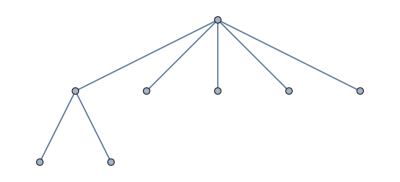
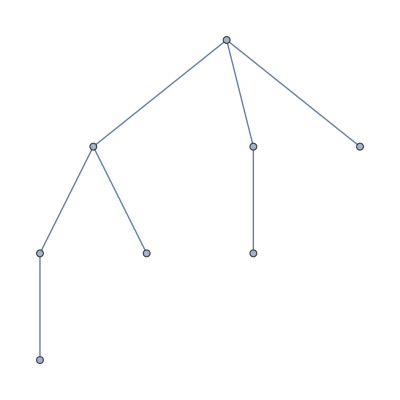
{{{0,0.0139452,0,0.010627,0,0.999003,0,0.0139408,0,0.0213517,0,0.0163863,0,0.0277026,0,0.000388192},{0,-0.0047598,0,-0.00651162,0,0.037825,0,-0.00167356,0,-0.609354,0,-0.566302,0,-0.553541,0,-0.00914759},{0,0.0157436,0,0.0326808,0,0.00754591,0,0.0159923,0,-0.0086496,0,0.703126,0,-0.709867,0,1.32811×10^-6},{0,0.032702,0,-0.00494092,0,0.00204471,0,-0.0231598,0,0.791776,0,-0.427917,0,-0.433503,0,-0.0204464},{0,-0.427917,0,-0.791776,0,0.0204464,0,-0.433503,0,0.00494092,0,0.032702,0,-0.0231598,0,-0.00204471},{0,-0.703126,0,-0.0086496,0,1.32811×10^-6,0,0.709867,0,0.0326808,0,-0.0157436,0,-0.0159923,0,0.00754591},{0,-0.566302,0,0.609354,0,0.00914759,0,-0.553541,0,0.00651162,0,-0.0047598,0,-0.00167356,0,-0.037825},{0,-0.0163863,0,0.0213517,0,0.000388192,0,-0.0277026,0,0.010627,0,-0.0139452,0,-0.0139408,0,0.999003},{0.000693374,0,0.049167,0,0.0298897,0,0.0385403,0,0.0139231,0,0.997348,0,0.0106273,0,0.0139365,0},{0.00912191,0,0.550719,0,0.566878,0,0.608817,0,0.000601604,0,-0.0677622,0,0.00414515,0,0.00277697,0},{2.00638×10^-6,0,-0.71063,0,0.702829,0,-0.0102732,0,0.0110217,0,0.0138225,0,0.022408,0,0.0108166,0},{-0.0204521,0,-0.434437,0,-0.427744,0,0.791901,0,-0.0156904,0,0.00359094,0,-0.00341332,0,0.0224268,0},{0.00359094,0,0.0156904,0,-0.0224268,0,-0.00341332,0,0.434437,0,-0.0204521,0,0.791901,0,0.427744,0},{-0.0138225,0,0.0110217,0,0.0108166,0,-0.022408,0,-0.71063,0,-2.00638×10^-6,0,0.0102732,0,0.702829,0},{0.0677622,0,0.000601604,0,0.00277697,0,-0.00414515,0,0.550719,0,-0.00912191,0,-0.608817,0,0.566878,0},{-0.997348,0,0.0139231,0,0.0139365,0,-0.0106273,0,0.049167,0,-0.000693374,0,-0.0385403,0,0.0298897,0}},{-Graphics-,-Graphics-},SparseArray[…]}

```mathematica
{utit4,dtit4,ztit4}=Chop[blockDiagonalizeMurota[gtit4sa]]
```

```mathematica
Chop[Table[utit4.gtit4sa[[i]].utit4†//MatrixForm,{i,Length[gtit4sa]}],10^(-7)]
```

{(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 356.782 | 344.003 | -70.6052 | -17.8547 | -0.0433717 | -0.0123425 | -0.000282135 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 344.003 | 699.732 | 2.8922 | 0.730117 | -1.27256 | -0.324519 | 0 | 0.000027495
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -70.6052 | 2.8922 | 128.041 | -0.147616 | -1.04175 | 0 | 0.0584599 | 0.000216679
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17.8547 | 0.730117 | -0.147616 | 53.9567 | 0 | -0.437303 | -0.0962308 | -0.000319624
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0433717 | -1.27256 | -1.04175 | 0 | 0.0567793 | -0.00269919 | 0.00240497 | -0.00573148
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0123425 | -0.324519 | 0 | -0.437303 | -0.00269919 | 0.0276424 | -0.00399912 | 0.00951414
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.000282135 | 0 | 0.0584599 | -0.0962308 | 0.00240497 | -0.00399912 | 0.00772931 | -0.0083505
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000027495 | 0.000216679 | -0.000319624 | -0.00573148 | 0.00951414 | -0.0083505 | 0.0168949),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16873.5 | -825.775 | 169.487 | 42.8599 | 0.104113 | 0.029628 | 0.000677263 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -825.775 | 48.1404 | -6.9427 | -1.75264 | 3.05477 | 0.779005 | 0 | -0.0000660015
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 169.487 | -6.9427 | 3.8985 | 0.354351 | 2.50072 | 0 | -0.140333 | -0.000520135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 42.8599 | -1.75264 | 0.354351 | 1.13661 | 0 | 1.04974 | 0.231001 | 0.000767253
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.104113 | 3.05477 | 2.50072 | 0 | 5.55514 | 0.00647938 | -0.00577312 | 0.0137584
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.029628 | 0.779005 | 0 | 1.04974 | 0.00647938 | 2.32278 | 0.00959985 | -0.0228386
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000677263 | 0 | -0.140333 | 0.231001 | -0.00577312 | 0.00959985 | 0.411831 | 0.0200453
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0000660015 | -0.000520135 | 0.000767253 | 0.0137584 | -0.0228386 | 0.0200453 | 0.00138647),(16909.4 | 318.956 | 68.2281 | 17.3189 | 0.00443096 | 0.00126137 | 0.0000292245 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
318.956 | 13.7401 | -0.12158 | -0.0307245 | 3.02983 | 0.768795 | 0 | 1.19234×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68.2281 | -0.12158 | 2.54051 | -0.00633165 | -2.54382 | 0 | 0.137647 | -9.21409×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17.3189 | -0.0307245 | -0.00633165 | 1.07367 | 0 | -1.06616 | -0.227358 | 0.0000135658 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00443096 | 3.02983 | -2.54382 | 0 | 5.47588 | -0.00028099 | 0.000244128 | 0.00561442 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00126137 | 0.768795 | 0 | -1.06616 | -0.00028099 | 2.29543 | -0.000404884 | -0.00927008 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0000292245 | 0 | 0.137647 | -0.227358 | 0.000244128 | -0.000404884 | 0.411249 | 0.00775905 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.19234×10^-6 | -9.21409×10^-6 | 0.0000135658 | 0.00561442 | -0.00927008 | 0.00775905 | 0.000330325 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(335.518 | -333.22 | -71.2795 | -18.0934 | -0.00462913 | -0.00131778 | -0.0000305316 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-333.22 | 720.082 | 0.127018 | 0.0320986 | -3.16533 | -0.803178 | 0 | -1.24567×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-71.2795 | 0.127018 | 128.842 | 0.00661482 | 2.65758 | 0 | -0.143804 | 9.62617×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-18.0934 | 0.0320986 | 0.00661482 | 53.9904 | 0 | 1.11384 | 0.237526 | -0.0000141725 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00462913 | -3.16533 | 2.65758 | 0 | 0.11482 | 0.000293557 | -0.000255046 | -0.00586551 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00131778 | -0.803178 | 0 | 1.11384 | 0.000293557 | 0.0477105 | 0.000422991 | 0.00968467 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0000305316 | 0 | -0.143804 | 0.237526 | -0.000255046 | 0.000422991 | 0.00826242 | -0.00810606 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1.24567×10^-6 | 9.62617×10^-6 | -0.0000141725 | -0.00586551 | 0.00968467 | -0.00810606 | 0.0175211 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
tensorGHZH
```

SparseArray[…]

```mathematica
mpsToMpdoH[tensorGHZH]//MatrixForm
```

((1 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1))

```mathematica
Table[generators[mpsToMpdoH[tensorGHZH],2][[i,j]],{i,4},{j,4}]//MatrixForm
```

((1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1))

```mathematica
gGHZ[p_]:=makeSelfAdjoint[Table[generators[mpsToMpdoH[tensorGHZH],p][[Quotient[i+3,4],Mod[i,4]+1]],{i,16}],{}];
```

```mathematica
gGHZ[2]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
{uGHZ,dimGHZ,zGHZ}=blockDiagonalizeMurota[gGHZ[2]]
```

{{{-0.20432-0.444801 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.872012+0. ⅈ},{-0.363994-0.79241 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.489484+0. ⅈ},{1.11022×10^-16+0. ⅈ,0.+0. ⅈ,-0.417419+0.908714 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},{-Graphics-,-Graphics-},SparseArray[…]}

```mathematica
Chop[Table[uGHZ.gGHZ[2][[i]].uGHZ†//MatrixForm,{i,Length[gGHZ[2]]}],10^(-7)]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.239594 | 0.426836 | 0 | 0
0.426836 | 0.760406 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.178169 | 0.108698-0.454357 ⅈ | 0 | 0
0.108698+0.454357 ⅈ | -0.178169 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-0.387872 | -0.236634-0.208709 ⅈ | 0 | 0
-0.236634+0.208709 ⅈ | 0.387872 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.387872 | 0.236634+0.208709 ⅈ | 0 | 0
0.236634-0.208709 ⅈ | -0.387872 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.760406 | -0.426836 | 0 | 0
-0.426836 | 0.239594 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
tensorGHZChainH[l_]:=tensorChainH[mpsToMpdoH[tensorGHZH],l];
```

```mathematica
spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],p]//MatrixForm
```

((1-p | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | p)
(0 | 0 | 0 | 0
0 | 1-p | 0 | 0) | (0 | 0 | p | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | p | 0 | 0) | (0 | 0 | 1-p | 0
0 | 0 | 0 | 0)
(p | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1-p))

```mathematica
generators[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],p],2]//MatrixForm
```

(((1-p)^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | p^2 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | ((1-p) p | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (1-p) p | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (1-p)^2
0 | 0 | 0 | 0
0 | p^2 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (1-p) p
0 | 0 | 0 | 0
0 | (1-p) p | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (1-p) p | 0
0 | 0 | 0 | 0
(1-p) p | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | p^2 | 0
0 | 0 | 0 | 0
(1-p)^2 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | (1-p) p | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (1-p) p) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | p^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (1-p)^2))

```mathematica
ord = {2,3,1,4};
```

```mathematica
genSWI = generators[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],p],2];
```

```mathematica
Table[genSWI[[i,j]][[ord,ord]],{i,4},{j,4}]//MatrixForm
```

((0 | 0 | 0 | 0
0 | p^2 | 0 | 0
0 | 0 | (1-p)^2 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | (1-p) p | 0 | 0
0 | 0 | (1-p) p | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
p^2 | 0 | 0 | 0
0 | 0 | 0 | (1-p)^2
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
(1-p) p | 0 | 0 | 0
0 | 0 | 0 | (1-p) p
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (1-p) p | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (1-p) p | 0) | (0 | p^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (1-p)^2 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
((1-p) p | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (1-p) p) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (p^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (1-p)^2))

```mathematica
generators[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],0.25],1]//MatrixForm
```

((0.75 | 0.
0. | 0.) | (0. | 0.
0. | 0.) | (0. | 0.
0. | 0.) | (0.25 | 0.
0. | 0.)
(0. | 0.
0. | 0.) | (0. | 0.75
0. | 0.) | (0. | 0.25
0. | 0.) | (0. | 0.
0. | 0.)
(0. | 0.
0. | 0.) | (0. | 0.
0.25 | 0.) | (0. | 0.
0.75 | 0.) | (0. | 0.
0. | 0.)
(0. | 0.
0. | 0.25) | (0. | 0.
0. | 0.) | (0. | 0.
0. | 0.) | (0. | 0.
0. | 0.75))

```mathematica
Table[generators[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],0.25],2][[Quotient[i+3,4],Mod[i,4]+1]],{i,16}]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
gSwGHZ[k_]:=makeSelfAdjoint[Table[generators[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],0.25],k][[Quotient[i+3,4],Mod[i,4]+1]],{i,16}],{}];
```

```mathematica
gSwGHZ[2]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
{uSwGHZ,dimSwGHZ,zSwGHZ}=blockDiagonalizeMurota[gSwGHZ[2]]
```

{{{0.119446+0.492577 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.862033+0. ⅈ},{0.203149+0.837754 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.506852+0. ⅈ},{0.+5.55112×10^-17 ⅈ,0.195268-0.833568 ⅈ,0.503642-0.115667 ⅈ,0.+0. ⅈ},{5.55112×10^-17+1.11022×10^-16 ⅈ,-0.117862+0.503133 ⅈ,0.834412-0.191633 ⅈ,0.+0. ⅈ}},{-Graphics-,-Graphics-},SparseArray[…]}

```mathematica
tensorSwGHZChainH[l_]:=tensorChainH[spinWave[mpsToMpdoH[tensorGHZH],KroneckerProduct[sigmaX,sigmaX],0.25],l];
```

```mathematica
Chop[Table[gSwGHZ[2][[i]]//MatrixForm,{i,Length[gSwGHZ[2]]}],10^(-7)]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.1875 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0.1875 | 0
0 | 0 | 0 | 0),(0.5625 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0.0625 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0.28125
0 | 0 | 0.03125 | 0
0 | 0.03125 | 0 | 0
0.28125 | 0 | 0 | 0),(0 | 0 | 0 | 0.+0.28125 ⅈ
0 | 0 | 0.-0.03125 ⅈ | 0
0 | 0.+0.03125 ⅈ | 0 | 0
0.-0.28125 ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0.09375
0 | 0 | 0.09375 | 0
0 | 0.09375 | 0 | 0
0.09375 | 0 | 0 | 0),(0 | 0 | 0 | 0.+0.09375 ⅈ
0 | 0 | 0.-0.09375 ⅈ | 0
0 | 0.+0.09375 ⅈ | 0 | 0
0.-0.09375 ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0.-0.09375 ⅈ
0 | 0 | 0.+0.09375 ⅈ | 0
0 | 0.-0.09375 ⅈ | 0 | 0
0.+0.09375 ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0.-0.28125 ⅈ
0 | 0 | 0.+0.03125 ⅈ | 0
0 | 0.-0.03125 ⅈ | 0 | 0
0.+0.28125 ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0.0625 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0.5625),(0 | 0 | 0 | 0
0 | 0.1875 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0.1875)}

```mathematica
MatrixRank[Chop[Table[Flatten[gSwGHZ[2][[i]]],{i,Length[gSwGHZ[2]]}],10^(-7)]]
```

8

```mathematica
Chop[Table[uSwGHZ.gSwGHZ[2][[i]].uSwGHZ†//MatrixForm,{i,Length[gSwGHZ[2]]}],10^(-7)]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0.0481686 | 0.0819231 | 0 | 0
0.0819231 | 0.139331 | 0 | 0
0 | 0 | 0.0500689 | 0.0829519
0 | 0 | 0.0829519 | 0.137431),(0.144506 | 0.245769 | 0 | 0
0.245769 | 0.417994 | 0 | 0
0 | 0 | 0.0166896 | 0.0276506
0 | 0 | 0.0276506 | 0.0458104),(0.0579186 | 0.0322255-0.273329 ⅈ | 0 | 0
0.0322255+0.273329 ⅈ | -0.0579186 | 0 | 0
0 | 0 | 0.0121726 | 0.0064099-0.0280589 ⅈ
0 | 0 | 0.0064099+0.0280589 ⅈ | -0.0121726),(-0.238847 | -0.132893-0.0662801 ⅈ | 0 | 0
-0.132893+0.0662801 ⅈ | 0.238847 | 0 | 0
0 | 0 | -0.0248271 | -0.0130736-0.0137572 ⅈ
0 | 0 | -0.0130736+0.0137572 ⅈ | 0.0248271),(0.0193062 | 0.0107418-0.0911095 ⅈ | 0 | 0
0.0107418+0.0911095 ⅈ | -0.0193062 | 0 | 0
0 | 0 | 0.0365179 | 0.0192297-0.0841768 ⅈ
0 | 0 | 0.0192297+0.0841768 ⅈ | -0.0365179),(-0.0796157 | -0.0442976-0.0220934 ⅈ | 0 | 0
-0.0442976+0.0220934 ⅈ | 0.0796157 | 0 | 0
0 | 0 | -0.0744813 | -0.0392207-0.0412715 ⅈ
0 | 0 | -0.0392207+0.0412715 ⅈ | 0.0744813),(0.0796157 | 0.0442976+0.0220934 ⅈ | 0 | 0
0.0442976-0.0220934 ⅈ | -0.0796157 | 0 | 0
0 | 0 | 0.0744813 | 0.0392207+0.0412715 ⅈ
0 | 0 | 0.0392207-0.0412715 ⅈ | -0.0744813),(0.238847 | 0.132893+0.0662801 ⅈ | 0 | 0
0.132893-0.0662801 ⅈ | -0.238847 | 0 | 0
0 | 0 | 0.0248271 | 0.0130736+0.0137572 ⅈ
0 | 0 | 0.0130736-0.0137572 ⅈ | -0.0248271),(0.417994 | -0.245769 | 0 | 0
-0.245769 | 0.144506 | 0 | 0
0 | 0 | 0.0458104 | -0.0276506
0 | 0 | -0.0276506 | 0.0166896),(0.139331 | -0.0819231 | 0 | 0
-0.0819231 | 0.0481686 | 0 | 0
0 | 0 | 0.137431 | -0.0829519
0 | 0 | -0.0829519 | 0.0500689)}

```mathematica
MatrixRank[Chop[Flatten[cX[{2,1,1},{{1},{1},{1}},uSwGHZ†,tensorSwGHZChainH,2],{{1,6,2},{3,4,5}}]]]
```

12

```mathematica
4(2^2-1)
```

12